# Thesis Notebook

## 2D Orbit now with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions

### r(r̄) and r̄(r) functions

```mathematica
(*Block function says use this value of M then forget it*)

rSchw[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2]; 

rBarSchw[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])];
```

### Lapse and shift

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2];
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))];
```

## TOV ρ=constant Isotropic coords definitions

### Setting up Everything:

```mathematica
Mfunc[r_] = Piecewise[{{M r^3/RStar^3, r <= RStar}, {M, r>RStar}}];
grrTOV[r_] = (1 - (2Mfunc[r])/r)^-1; 
κ = √(2 M/RStar^3);
(*Integral constant I used by hand*)
Const = rBarSchw[RStar] √((1+√(1-(2M)/RStar))/(1-√(1-2 M/RStar))); (*Can use schw to convert RStar as the value should be the same inside and outside*) (*This is the constant to match up the metrics*)
```

#### Schwarzschild and Isotropic interior coordinate conversion formulas

```mathematica
rBarofrInside[r_]=Const √((1-√(1-2 Mfunc[r]/r))/(1+√(1-2 Mfunc[r]/r)));
rofRbarInside[R_]=1/κ √(1-Tanh[Log[R/Const]]^2);
```

#### Lapse and shift functions of the ρ=constant TOV metric:

```mathematica
αInside[rbar_]=(3/2 √(1-2 M/RStar)-1/2 √(1-2(M r^2)/RStar^3))/.r->rofRbarInside[rbar]; (*Lapse*)
AInside[rbar_]=rofRbarInside[rbar]/rbar;(*Shift*)
```

## Setting up new 2D ODEs with drag of course...

### Setting up constants and functions used

```mathematica
m = 10^-6; (*mass of PBH?*)
Ivariable = 10; 
ρ = 10;
a = 0.5; (*relativistic sound speed*)
```

```mathematica
P[rbar_] = ρ((√(1 - 2(M r^2)/RStar^3)-√(1 - 2 M/RStar))/(3 √(1 - 2 M/RStar) - √(1 - 2(M r^2)/RStar^3))) /.r->rofRbarInside[rbar];
(*Derived from TOV as I done last year*)
```

### Setting up ODEs

#### Mach Number business

```mathematica
IVariable[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 1},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1}
}];
(*Approximate Log[Λ] ~ 10 following other authors [9] on 2404]*)
```

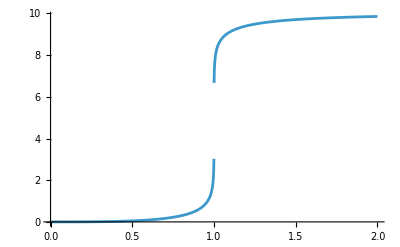

```mathematica
Plot[IVariable[Mach], {Mach, 0, 2},
PlotRange->All, Exclusions-> {Mach==1}]
```

Interpolating

```mathematica
x1 = 1;
x2 = 1;
y1 = 3.03;
y2 = 6.67;

anaylticline[Μach_] := y1 + (y2 - y1) (x - x1)/(x2 - x1);
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.9999},
{anaylticline[Μach], 0.9999 < Μach  < 1.0001},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.0001}
}];
```

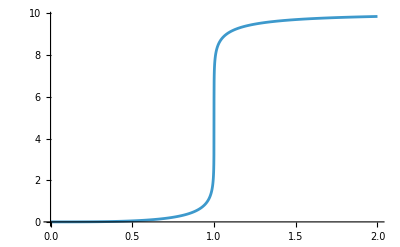

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, PlotRange->All, Exclusions->None]
```

#### Outside Star

```mathematica
Ut[rbar_, ur_, uphi_] = (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];

drBardt[rbar_, ur_, uphi_] = 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] = 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_, ur_, uphi_] = -α[rbar] Ut[rbar, ur, uphi] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur, uphi]((Derivative[1][A][rbar])/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + (Derivative[1][A][rbar])/(rbar^2*A[rbar]^3));
```

#### Inside Star

```mathematica
UtInside[rbar_, ur_, uphi_] = (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagphi[rbar_, ur_, uphi_] = (√(ur^2+(uphi/rbar)^2))/AInside[rbar];(*paper eqn ut and umagphi*)

drBardtInside[rbar_, ur_, uphi_] = 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] = 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;

(*Mach stuff*)

Mach[rbar_, ur_, uphi_] := Piecewise[{
{umagphi[rbar, ur, uphi]/(a α[rbar] Ut[rbar, ur, uphi]), rbar < rbarStar},
{umagphi[rbar, ur, uphi]/(a αInside[rbar] UtInside[rbar, ur, uphi]), rbar >= rbarStar}
}]

(*Accretion stuff*)

(* for Γ = 2 accretion rate*) (*This is my dmdt equation*)

mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi ρ m^2)/(a^2 + (umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2);


dpdtaccretionr[m_, rbar_, ur_, uphi_, λGR_, q_] := -(4 Pi αInside[rbar] λGR(ρ + P[rbar])m^2)/a^3(a^2/(a^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_, λGR_, q_] := -(4 Pi αInside[rbar] λGR(ρ + P[rbar])m^2)/a^3(a^2/(a^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)uphi


dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagphi[rbar, ur, uphi]^3(-4π αInside[rbar]*(ρ + P[rbar])*m^2*(1 + 2 umagphi[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtdragphi[rbar, ur, uphi] + dpdtaccretionphi[rbar, ur, uphi, λGR=1.49*a, q=2]);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 umagphi[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagphi[rbar, ur, uphi]^3;

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur, uphi]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + (Derivative[1][AInside][rbar])/(rbar^2 AInside[rbar]^3)) +  η/m(dpdtdragr[rbar, ur, uphi]+ dpdtaccretionr[rbar, ur, uphi, λGR=1.49*a, q=2]);
```

Defining Mach number business

```mathematica
Μ[rbar_, ur_, uphi_] := Piecewise[{
{umagphi[rbar, ur, uphi]/(a α[rbar] Ut[rbar, ur, uphi]), rbar < rbarStar},
{umagphi[rbar, ur, uphi]/(a αInside[rbar] UtInside[rbar, ur, uphi]), rbar >= rbarStar}
}]
```

#### Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

Speed up factor

```mathematica
η= 20; (*Speed up parameter 72.5 is nice*)
```

Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rBarSchw[r0];
rbarStar = rBarSchw[RStar];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
t0=0;
tEnd=2000;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[0]== rbar0,
ur[0]==0,
phi[0]==0,
uphi[0]==AngularMomentumUphi0,
mass[0] == m,

WhenEvent[rbar[t] <= 10^-3 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->20000
][[1]];
```

NDSolve::ndsz: At t == 1525.92, step size is effectively zero; singularity or stiff system suspected.

“u” causing problems as velocities go to zero.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

1525.92

160.867

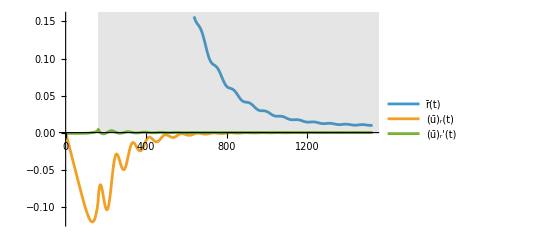

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

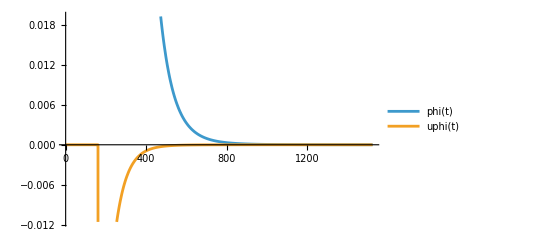

```mathematica
outFigAngular=Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

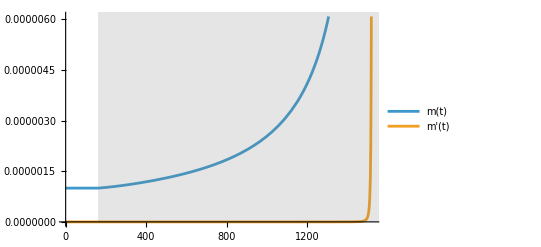

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

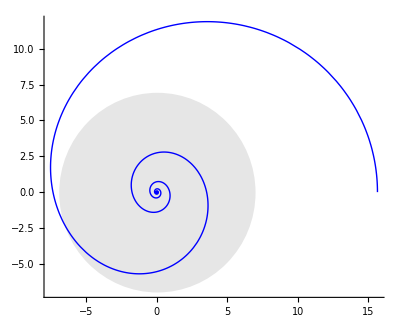

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

eccentric orbit and dig thru literature for u cubed and input speed factor.

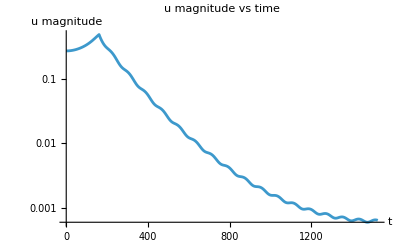

```mathematica
LogPlot[Evaluate[umagphi[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
(*Show me the value of u at tfinish*)
umagphi[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn;
```

#### Converting back to the areal radius to see the graphs and if it is different

```mathematica
(*Areal radius as a function of isotropic radius*)rFromRbar[rbar_]:=Piecewise[{{A[rbar]*rbar,rbar>=rbarStar},(*exterior*){AInside[rbar]*rbar,rbar<rbarStar}    (*interior*)}];

(*Areal radius along the orbit*)
arealr[t_]:=rFromRbar[rbarNumIn[t]];
```

```mathematica
x[t_]:=arealr[t] Cos[phiNumIn[t]];
y[t_]:=arealr[t] Sin[phiNumIn[t]];
```

```mathematica
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->1,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
```

```mathematica
(*Areal radius of the stellar surface*)
rstarAreal=A[rbarStar] rbarStar;

centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rstarAreal]}];
```

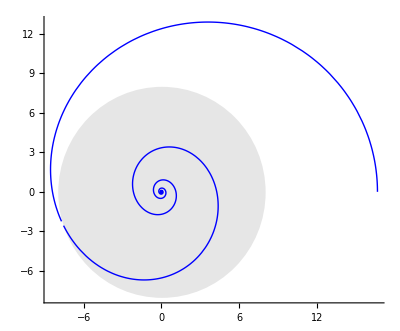

```mathematica
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

discontinuity here at the edge, not sure why?

## Capturing the PBH from infinity

Assuming PBH comes from infinity and just hits in and enters the star

#### Approaching the problem differently, using Keplerian orbits on the outside of the star and then GR on the inside to reduce the stiffness of the problem causing the error in the solver.

Setting v_inf to something physical is essential, most dark matter comes from the galactic halo, where things move at roughly 200km/s so with setting c = 1, vinf should be 10^-3 which implies the Energy at infinity should be approximately equal to 1 and very little energy loss is needed to bound the orbit.

#### Defining Initial Data Functions

```mathematica
vinf = 10^-3;
```

```mathematica
InitialEnergyAtInfinity[vinf_] := 1/(√(1 - vinf^2)); (*eq47 2404 paper*)
```

```mathematica
(*general formula for the magnitude of the velocity, for a general spherically symmetric Isotropic metric*)
umagVel[ur_, uphi_, rbar_] := √(ur^2 + (uphi/rbar)^2)
umagE[Energy_, rbar_] := A[rbar] √((Energy/α[rbar])^2 - 1); (*eq 48 in paper*)
```

```mathematica
(*Defining the Impact angle, which is the angle between the radial vector and the PBH's velocity vector*) (*It is the angle the PBH enters the star*)

urInit[psi_, Einit_] := -umagE[Einit , rbarStar]Cos[psi];
uphiInit[psi_, rbarStar_, Einit_] := rbarStar umagE[Einit ]Sin[psi]; (*Is defining angular momentum, L is equal to this*)
```

#### Setting the Initial conditions

```mathematica
(*we start at rbarStar*)
phi0 = 0;
Einf = InitialEnergyAtInfinity[vinf];
 u = umagE[Einf, rbarStar];
ImpactAngle = Pi/4; (*In radians, measured from center of star to the position of particle, in unit circle fashion, pi/2 corresponds to grazing the star as it enters and 0 corresponds to a radial drop*)
ur0 = -u*Cos[ImpactAngle];
uphi0 = (rbarStar)(u) Sin[ImpactAngle];
```

#### Sanity Check to see if the two energy formulas match up

```mathematica
Einf = InitialEnergyAtInfinity[vinf] //N
α[rbarStar]^2  Ut[rbarStar, ur0, uphi0] //N (*This Ut was upper indexed*)
```

1.

1.

#### Performing the inside integration

```mathematica
t0=0;
tEnd=10000;

solIn=NDSolve[
{
rbar'[t]==
If[
rbar[t] >=rbarStar,
drBardt[rbar[t],ur[t],uphi[t]],
drBardtInside[rbar[t],ur[t],uphi[t]]
],
ur'[t]==
If[
rbar[t] >=rbarStar,
durdt2DOutside[rbar[t],ur[t],uphi[t]],durdt2DInside[rbar[t],ur[t],uphi[t]]
],
uphi'[t]==
If[
rbar[t] >= rbarStar,
0,
duphidtInside[rbar[t],ur[t],uphi[t]]
],
phi'[t]==
If[
rbar[t] >= rbarStar,
dphidtOutside[rbar[t],ur[t],uphi[t]],dphidtInside[rbar[t],ur[t],uphi[t]]
],
rbar[0]==rbarStar,
ur[0]==ur0,
uphi[0]==uphi0,
phi[0]==phi0,

WhenEvent[
rbar[t] - rbarStar >0 && ur[t] >0,
"StopIntegration"
] (*Stop Integration if the PBH exits the star again*)
},
{rbar,ur,uphi,phi},{t,t0,tEnd},

WorkingPrecision->40,
MaxSteps->20000, 
Method->{"StiffnessSwitching"}
][[1]];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (-7-4 √3)+1/2 (7+4 √3).

Round::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Round[Sign[1/2 (-7-4 √3)+1/2 (7+4 √3)]].

NDSolve::ndinid: Initial condition Sign[1/2 (-7-4 √3)+1/2 (7+4 √3)] is not in the range specified by the discrete variable NDSolve`s$66936.

Notes for next meeting

- Went through papers using ctrl F and also put them through, couldnt see anything to help with 1/u^3
- added in the epsilon to fix the issue, worked and got to the centre, although abruptly, maybe I can just turn off the drag if it becomes less important or something
- looked at PBH coming from infinity and got that setup as in paper, although issue with singularity persisted